--- Initializing MHG Permutation Tree ---

✓ Vault evidence loaded.

--- STEP 1: Identifying Analytical Dimensions ---

[Validated] 3 dimensions identified:

Affected Population: Primarily Navajo, General Population

Agent Type: Biological Pathogen, Chemical Toxin

Exposure Origin: Natural Environmental, Accidental Human-Caused, Intentional Human-Caused

--- STEP 2: Generating All Permutations ---

Total permutations before scoring: 12

--- STEP 3: Scoring Permutations ---

[Validated] 12 permutations scored.

Kept: 10 | Discarded: 2

Final hypotheses (survivors):

H1: The acute respiratory illness and deaths in the Four Corners region are caused by a naturally occurring biological pathogen primarily affecting the Navajo population.

H2: The acute respiratory illness and deaths in the Four Corners region are caused by a naturally occurring biological pathogen affecting the general population.

H3: The acute respiratory illness and deaths in the Four Corners region are caused by an accidentally released biological pathogen primarily affecting the Navajo population.

H4: The acute respiratory illness and deaths in the Four Corners region are caused by an accidentally released chemical toxin primarily affecting the Navajo population.

H5: The acute respiratory illness and deaths in the Four Corners region are caused by a naturally occurring chemical toxin primarily affecting the Navajo population.

✓ Hypotheses exported to Vault.

✓ Scoring table saved to Vault/permutation_scores.md

--- STEP 4: Building Permutation Tree ---

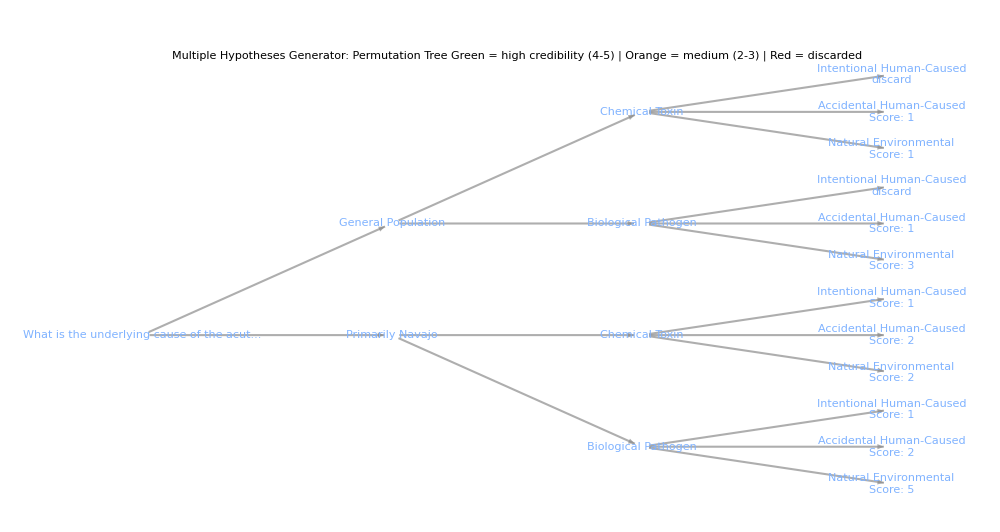

✓ Permutation tree exported to Vault.

```mathematica
(* ============================================================*)(*01.5:Multiple Hypotheses Generator-Permutation Tree*)(* ============================================================*)

Get[NotebookDirectory[]<>"Core_API_Functions.wl"];
Print["--- Initializing MHG Permutation Tree ---"];

numberedEvidence=Import[$vaultDir<>"evidence_vault.md","Text"];
Print["✓ Vault evidence loaded."];

centralQuestionFile=$vaultDir<>"central_question.md";
centralQuestionContext=If[FileExistsQ[centralQuestionFile],"The central analytical question for this case is:\n"<>StringReplace[Import[centralQuestionFile,"Text"],"# Central Analytical Question\n\n"->""]<>"\n\n",""];

(* ============================================================*)
(*STEP 1:Identify analytical dimensions*)
(* ============================================================*)
Print["\n--- STEP 1: Identifying Analytical Dimensions ---"];

dimensionPrompt="You are an expert intelligence analyst applying the Multiple "<>"Hypotheses Generator (MHG) from Beebe & Pherson (2015).\n\n"<>centralQuestionContext<>"Identify the 2-3 most analytically useful component dimensions "<>"for this case. The most useful are ones like:\n"<>"- WHO is affected or responsible?\n"<>"- WHAT is the mechanism or agent?\n"<>"- WHY / HOW did it happen (intentional, accidental, natural)?\n\n"<>"Pick dimensions where different answers lead to meaningfully "<>"different hypotheses. For each, provide 2-4 mutually exclusive options.\n\n"<>"Output ONLY valid JSON in exactly this structure:\n"<>"{\n"<>"  \"dimensions\": [\n"<>"    {\"name\": \"Who?\", \"options\": [\"Only Navajos\", \"Anyone\"]},\n"<>"    {\"name\": \"What?\", \"options\": [\"Common flu\", \"Unknown pathogen\", \"Chemical toxin\"]},\n"<>"    {\"name\": \"Why?\", \"options\": [\"Act of nature\", \"Intentional act\", \"Accidental exposure\"]}\n"<>"  ]\n"<>"}\n\n"<>"No markdown, no explanation, no extra keys. Raw JSON only.\n\n"<>"Evidence:\n"<>numberedEvidence;

rawDimensions=callGemini[dimensionPrompt,0.2];
cleanDimensions=StringTrim[rawDimensions];
cleanDimensions=StringReplace[cleanDimensions,{"```json\n"->"","```json"->"","```"->""}];
dimData=ImportString[cleanDimensions,"RawJSON"];

If[dimData===$Failed||!AssociationQ[dimData]||!KeyExistsQ[dimData,"dimensions"],Print["[ERROR] Failed to parse dimension JSON. Raw: "<>rawDimensions];
Abort[]];

dimensions=dimData["dimensions"];
Print["[Validated] "<>ToString[Length[dimensions]]<>" dimensions:"];
Do[Print["  "<>dimensions[[d]]["name"]<>": "<>StringJoin[Riffle[dimensions[[d]]["options"],", "]]],{d,Length[dimensions]}];

(* ============================================================*)
(*STEP 2:Generate all permutations*)
(* ============================================================*)
Print["\n--- STEP 2: Generating All Permutations ---"];

dimNames=Map[#["name"]&,dimensions];
optionLists=Map[#["options"]&,dimensions];

allCombinations=Tuples[optionLists];
numPermutations=Length[allCombinations];
Print["Total permutations before scoring: "<>ToString[numPermutations]];

permutationSentences=Map[Function[combo,StringJoin[Riffle[MapThread[(#1<>": "<>#2)&,{dimNames,combo}]," | "]]],allCombinations];

(* ============================================================*)
(*STEP 3:Score permutations*)
(* ============================================================*)
Print["\n--- STEP 3: Scoring Permutations ---"];

permutationBlock=StringJoin[MapIndexed[(ToString[#2[[1]]]<>". "<>#1<>"\n")&,permutationSentences]];

scoringPrompt="You are an expert intelligence analyst applying the Multiple "<>"Hypotheses Generator (MHG) from Beebe & Pherson (2015).\n\n"<>centralQuestionContext<>"Score each permutation 1-5 for credibility, or \"discard\" if "<>"logically contradictory or implausible given the evidence.\n\n"<>"Output ONLY a JSON array, one object per permutation, same order as input:\n"<>"[{\"permutation\": \"...\", \"score\": 3, "<>"\"hypothesis\": \"Plain English statement of this scenario.\"},\n"<>" {\"permutation\": \"...\", \"score\": \"discard\", \"hypothesis\": \"\"}]\n\n"<>"The hypothesis field is a single plain English sentence restating "<>"the permutation as a testable claim (e.g. \"People are dying from a "<>"naturally occurring unknown pathogen.\"). "<>"Leave empty string for discarded items.\n\n"<>"No markdown, no explanation. Raw JSON array only.\n\n"<>"Evidence:\n"<>numberedEvidence<>"\n\n"<>"Permutations to score:\n"<>permutationBlock;

rawScoring=callGemini[scoringPrompt,0.2];
cleanScoring=StringTrim[rawScoring];
cleanScoring=StringReplace[cleanScoring,{"```json\n"->"","```json"->"","```"->""}];
scoredData=ImportString[cleanScoring,"RawJSON"];

If[scoredData===$Failed||!ListQ[scoredData],Print["[ERROR] Failed to parse scoring JSON. Raw: "<>rawScoring];
Abort[]];
Print["[Validated] "<>ToString[Length[scoredData]]<>" permutations scored."];

keptPermutations=Select[scoredData,Function[p,p["score"]=!="discard"&&p["score"]=!=0&&StringQ[p["hypothesis"]]&&StringLength[p["hypothesis"]]>0]];

discardedPermutations=Select[scoredData,Function[p,p["score"]==="discard"||p["score"]===0]];

Print["Kept: "<>ToString[Length[keptPermutations]]<>" | Discarded: "<>ToString[Length[discardedPermutations]]];

keptPermutations=SortBy[keptPermutations,Function[p,-If[NumberQ[p["score"]],p["score"],0]]];

maxHypotheses=5;
finalHypotheses=MapIndexed[("H"<>ToString[#2[[1]]]<>": "<>#1["hypothesis"])&,Take[keptPermutations,UpTo[maxHypotheses]]];

Print["\nFinal hypotheses (survivors):"];
Do[Print["  "<>finalHypotheses[[i]]],{i,Length[finalHypotheses]}];

Export[$vaultDir<>"target_hypotheses.md",StringJoin[Riffle[finalHypotheses,"\n"]],"Text"];
Print["✓ Hypotheses exported to Vault."];

(*FIX:replace|in permutation strings so they don't break markdown columns*)
safePermutation[s_]:=StringReplace[s," | "->" / "];

Export[$vaultDir<>"permutation_scores.md","# MHG Permutation Scoring\n\n"<>"| # | Permutation | Score | Hypothesis |\n"<>"|---|---|---|---|\n"<>StringJoin[MapIndexed[("| "<>ToString[#2[[1]]]<>" | "<>safePermutation[#1["permutation"]]<>" | "<>ToString[#1["score"]]<>" | "<>#1["hypothesis"]<>" |\n")&,scoredData]],"Text"];
Print["✓ Scoring table saved to Vault/permutation_scores.md"];

(* ============================================================*)
(*STEP 4:Permutation Tree Visualization*)
(* ============================================================*)
Print["\n--- STEP 4: Building Permutation Tree ---"];

levelColors={GrayLevel[0.25],RGBColor[0.2,0.35,0.65],RGBColor[0.15,0.55,0.40],RGBColor[0.65,0.30,0.20],RGBColor[0.50,0.25,0.60]};

nodeStyle[label_,color_,w_]:=Framed[Style[label,9,FontFamily->"Helvetica",White,Bold,LineBreakWithin->True],Background->color,RoundingRadius->5,FrameStyle->None,ImageSize->{w,Automatic}];

leafStyle[label_,score_]:=Module[{color,scoreStr},color=Which[score==="discard",Darker[Red,0.4],NumberQ[score]&&score>=4,Darker[Green,0.35],NumberQ[score]&&score>=2,RGBColor[0.75,0.5,0.1],True,GrayLevel[0.5]];
scoreStr=If[score==="discard","discard","Score: "<>ToString[score]];
Framed[Column[{Style[label,8,FontFamily->"Helvetica",White,LineBreakWithin->True],Style[scoreStr,8,FontFamily->"Helvetica",If[score==="discard",Pink,Yellow],Bold]},Alignment->Left,Spacings->0.2],Background->color,RoundingRadius->4,FrameStyle->None,ImageSize->{150,Automatic}]];

rootLabel=If[FileExistsQ[centralQuestionFile],StringTrim[StringReplace[Import[centralQuestionFile,"Text"],"# Central Analytical Question\n\n"->""]],"Analytical Question"];
rootDisplay=If[StringLength[rootLabel]>40,StringTake[rootLabel,40]<>"...",rootLabel];

allNodes={"__ROOT__"};
allEdges={};
nodeLabels=<|"__ROOT__"->rootDisplay|>;
nodeTypes=<|"__ROOT__"->"root"|>;
nodeScores=<||>;

numDims=Min[Length[dimensions],3];
dim1Options=dimensions[[1]]["options"];

Do[d1=dim1Options[[i]];
nodeKey="D1_"<>d1;
AppendTo[allNodes,nodeKey];
AppendTo[allEdges,DirectedEdge["__ROOT__",nodeKey]];
nodeLabels[nodeKey]=d1;
nodeTypes[nodeKey]="dim1";,{i,Length[dim1Options]}];

If[numDims>=2,dim2Options=dimensions[[2]]["options"];
Do[d1=dim1Options[[i]];
Do[d2=dim2Options[[j]];
nodeKey="D1_"<>d1<>"|D2_"<>d2;
AppendTo[allNodes,nodeKey];
AppendTo[allEdges,DirectedEdge["D1_"<>d1,nodeKey]];
nodeLabels[nodeKey]=d2;
nodeTypes[nodeKey]=If[numDims==2,"leaf","dim2"];
If[numDims==2,matchedScore="discard";
Do[If[StringContainsQ[scoredData[[s]]["permutation"],d1]&&StringContainsQ[scoredData[[s]]["permutation"],d2],matchedScore=scoredData[[s]]["score"];Break[]],{s,Length[scoredData]}];
nodeScores[nodeKey]=matchedScore;];,{j,Length[dim2Options]}],{i,Length[dim1Options]}]];

If[numDims>=3,dim2Options=dimensions[[2]]["options"];
dim3Options=dimensions[[3]]["options"];
Do[d1=dim1Options[[i]];
Do[d2=dim2Options[[j]];
parentKey="D1_"<>d1<>"|D2_"<>d2;
Do[d3=dim3Options[[k]];
leafKey="D1_"<>d1<>"|D2_"<>d2<>"|D3_"<>d3;
AppendTo[allNodes,leafKey];
AppendTo[allEdges,DirectedEdge[parentKey,leafKey]];
nodeLabels[leafKey]=d3;
nodeTypes[leafKey]="leaf";
matchedScore="discard";
Do[If[StringContainsQ[scoredData[[s]]["permutation"],d1]&&StringContainsQ[scoredData[[s]]["permutation"],d2]&&StringContainsQ[scoredData[[s]]["permutation"],d3],matchedScore=scoredData[[s]]["score"];Break[]],{s,Length[scoredData]}];
nodeScores[leafKey]=matchedScore;,{k,Length[dim3Options]}],{j,Length[dim2Options]}],{i,Length[dim1Options]}]];

vertexShapeFunc=Function[{coords,name,size},Module[{ntype,label,score},ntype=Lookup[nodeTypes,name,"dim1"];
label=Lookup[nodeLabels,name,name];
score=Lookup[nodeScores,name,Missing[]];
Which[name==="__ROOT__",Inset[nodeStyle[label,GrayLevel[0.25],160],coords],ntype==="leaf",Inset[leafStyle[label,If[MissingQ[score],"discard",score]],coords],ntype==="dim1",Inset[nodeStyle[label,levelColors[[2]],130],coords],ntype==="dim2",Inset[nodeStyle[label,levelColors[[3]],120],coords],True,Inset[nodeStyle[label,levelColors[[4]],110],coords]]]];

imageH=Max[500,Length[allNodes]*28];

permTree=Graph[allNodes,allEdges,VertexShapeFunction->vertexShapeFunc,EdgeStyle->Directive[GrayLevel[0.55],AbsoluteThickness[1.5],Arrowheads[0.015]],GraphLayout->{"LayeredDigraphEmbedding","RootVertex"->"__ROOT__","Orientation"->Left},ImageSize->{1000,imageH},PlotLabel->Style["Multiple Hypotheses Generator: Permutation Tree\n"<>"Green = high credibility (4-5)  |  Orange = medium (2-3)  |  Red = discarded",Bold,12,FontFamily->"Helvetica"]];

permTree
Export[$vaultDir<>"Permutation_Tree_Master.pdf",permTree];
Print["✓ Permutation tree exported to Vault."];
```